```mathematica
<<"https://raw.githubusercontent.com/ruffinevans/SpectraFitting/master/SpectraFitting.m"
```

Usage Instructions:

1. Get a list of spectra from a directory by using the GetSpecDir[path] function.

2. (Optional) Get an individual spectrum for flatfield correction using the GetSpec[path] function. Divide each spectrum by this flat-field using the SpecDivide[spec,ffspec] function.

3. Initialize a list of guesses using the CoordInit[Spectra,center,d] function, where center is a very preliminary guess for the center point of a generic spectrum and d is the overall spread to zoom in on for further fitting. You should save this guess as a variable.

4. Use the PickGuesses[Spectra,CoordList] command to interactively refine these guesses. CoordList should be the variable you defined in the previous step.

5. Run SingleLorentzianFit[Spectra, Coordlist] to fit each function to a single Lorentzian. Save the output to a variable. More options are coming soon.

6. Use the ShowFits[Spectra, CoordList, Fits, Path] where Fits is the list of fits and Path is the original directory to display all of the fits and important parameters.


If you need additional help, all of the functions have usage instructions that can be queried with two question marks and the name of the function, e.g. ??ShowFits .

Directory where spectra reside. Should be tab separated files, but CSV will probably also work.

```mathematica
DataDir="C:\\Users\\LukinLab\\Documents\\Ruffin\\Dropbox\\Harvard Physics\\Lukin Lab\\Scripts and Programs\\Transmission Spectra\\Clean Code\\Example Data";
```

```mathematica
Spectra=GetSpecDir[DataDir];
```

Center wavelength to attempt fitting around, in nanometers. This is just a guess that will be confirmed later.

```mathematica
λcenter=650;
```

Maximum spread in guessed wavelengths. This is just to zoom in on the graphs so that the user can set the guess better.

```mathematica
Δλ=30;
```

Run this function to initialize the coordinate list.

```mathematica
CoordList=CoordInit[Spectra,λcenter,Δλ];
```

Drag the red circles on top of the peaks. Put the black marker on a background point. Put the two blue markers on either side of the peak you want to fit to constrain the fit. Only the horizontal coordinate matters.

```mathematica
PickGuesses[Spectra,CoordList]
```

{,,,,,,,,,,,,,,,,,}

```mathematica
fits=SingleLorentzianFit[Spectra,CoordList]
```

Fitting 1 out of 18

Fitting 2 out of 18

Fitting 3 out of 18

Fitting 4 out of 18

Fitting 5 out of 18

Fitting 6 out of 18

Fitting 7 out of 18

Fitting 8 out of 18

Fitting 9 out of 18

Fitting 10 out of 18

Fitting 11 out of 18

Fitting 12 out of 18

Fitting 13 out of 18

Fitting 14 out of 18

Fitting 15 out of 18

Fitting 16 out of 18

Fitting 17 out of 18

Fitting 18 out of 18

{FittedModel[1245.45/(1+37.8707 («1»)^2)],FittedModel[7268.17/(1+15.1171 («1»)^2)],FittedModel[7358.12/(1+38.0224 («1»)^2)],FittedModel[12067.9/(1+46.8145 («1»)^2)],FittedModel[13556.7/(1+36.7553 («1»)^2)],FittedModel[9805.14/(1+10.5904 («1»)^2)],FittedModel[12731.8/(1+15.4516 («1»)^2)],FittedModel[19586.4/(1+24.3152 («1»)^2)],FittedModel[20945.1/(1+13.1292 («1»)^2)],FittedModel[4879.05/(1+39.8943 («1»)^2)],FittedModel[2864.3/(1+46.6523 («1»)^2)],FittedModel[1910.42/(1+131.57 («1»)^2)],FittedModel[2424.03/(1+136.512 («1»)^2)],FittedModel[2595.72/(1+38.2993 («1»)^2)],FittedModel[2897.27/(1+38.0793 («1»)^2)],FittedModel[6687.72/(1+26.1353 («1»)^2)],FittedModel[6719.65/(1+27.8593 («1»)^2)],FittedModel[5596.88/(1+10.0036 («1»)^2)]}

FittedModel::constr: The property values {"ParameterErrors"} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::stop: Further output of FittedModel :: constr will be suppressed during this calculation.

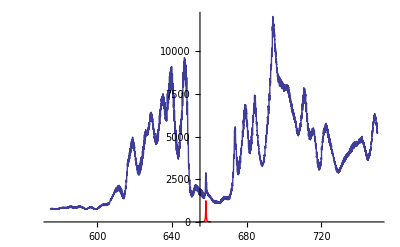
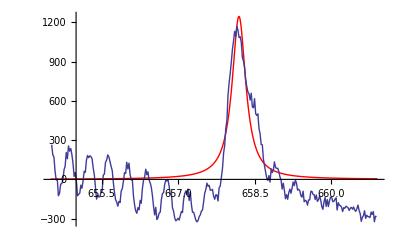
{10070_afterTE-1_0709a 17_36_26.csv, λ_center=658.188±0.0140224, γ_FWHM=0.162498±0.0099124, Q=2026.22±116.436,-Graphics-,-Graphics-}

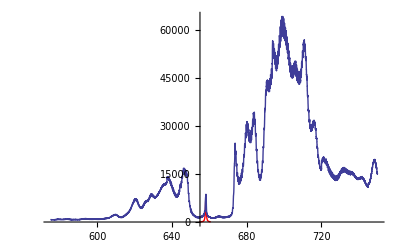
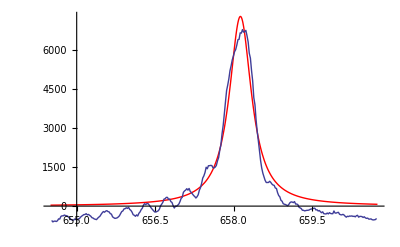
{10070_afterTE-1_0709a_realigned 17_40_07.csv, λ_center=658.13±0.00709092, γ_FWHM=0.257197±0.00500807, Q=1280.43±24.4368,-Graphics-,-Graphics-}

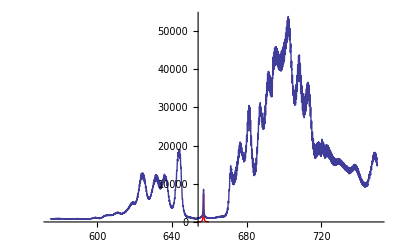
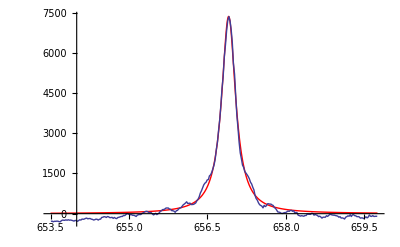
{10070_afterTE-1_0709b 17_42_56.csv, λ_center=656.905±0.00207871, γ_FWHM=0.162174±0.00146913, Q=2026.31±18.1826,-Graphics-,-Graphics-}

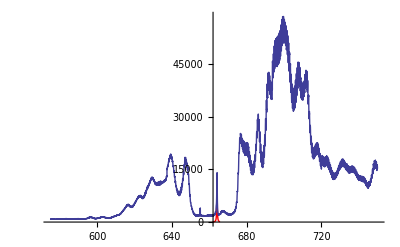
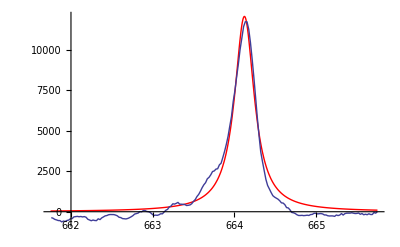
{10070_afterTE-1_0709c 17_44_39.csv, λ_center=664.122±0.00367557, γ_FWHM=0.146154±0.00259063, Q=2273.±39.5707,-Graphics-,-Graphics-}

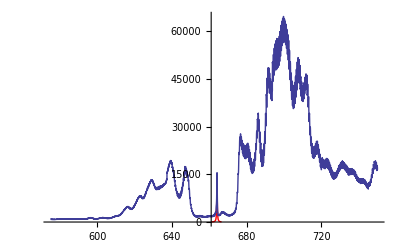
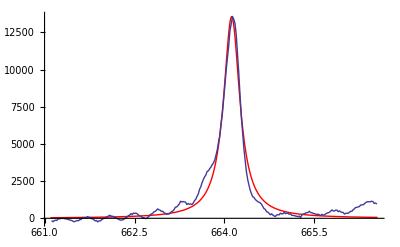
{10070_afterTE-1_0709c 17_47_08.csv, λ_center=664.12±0.00327569, γ_FWHM=-0.164945±0.00230959, Q=2012.15±28.5887,-Graphics-,-Graphics-}

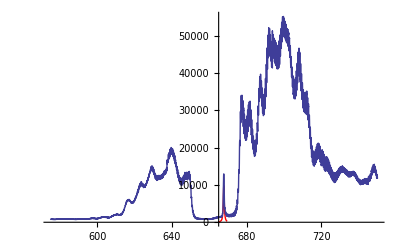
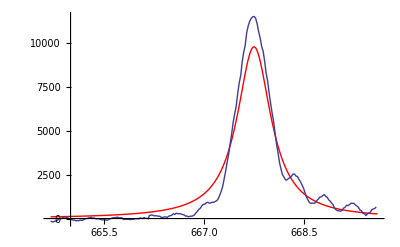
{10070_afterTE-1_0709d 17_50_43.csv, λ_center=667.75±0.00867496, γ_FWHM=0.307287±0.00610711, Q=1087.52±21.1731,-Graphics-,-Graphics-}

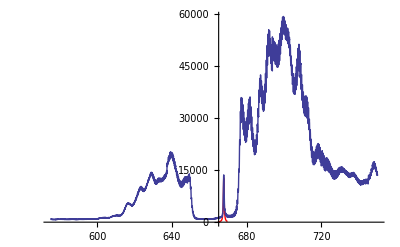
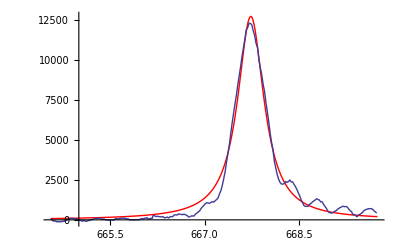
{10070_afterTE-1_0709d 17_52_21.csv, λ_center=667.735±0.00370587, γ_FWHM=0.254397±0.00261503, Q=1313.39±13.3532,-Graphics-,-Graphics-}

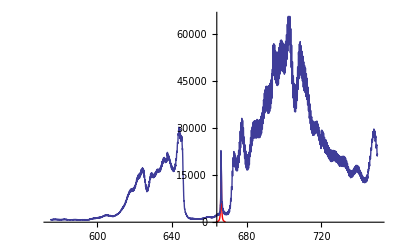
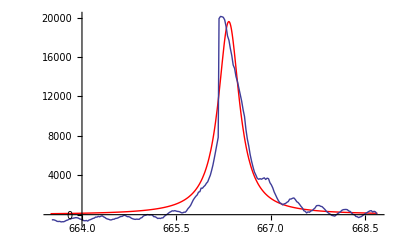
{10070_afterTE-1_0709e 17_54_14.csv, λ_center=666.336±0.00663881, γ_FWHM=0.202797±0.00467389, Q=1643.87±37.0104,-Graphics-,-Graphics-}

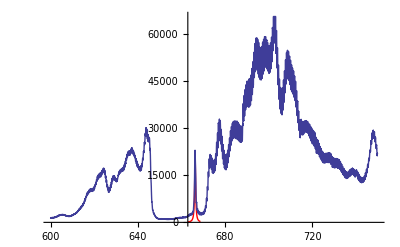
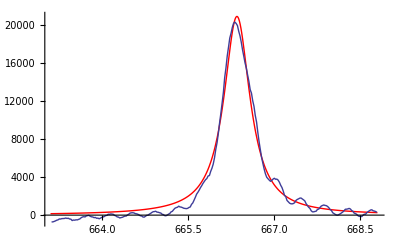
{10070_afterTE-1_0709e_600to750 17_55_18.csv, λ_center=666.35±0.0038975, γ_FWHM=0.275982±0.00274996, Q=1208.24±11.9106,-Graphics-,-Graphics-}

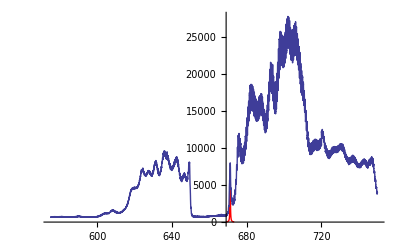
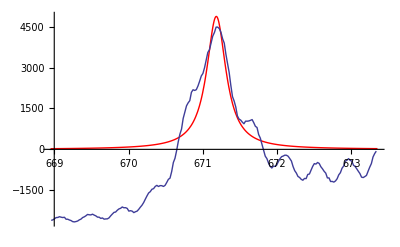
{10070_afterTE-1_0709f 17_25_24.csv, λ_center=671.181±0.0295063, γ_FWHM=-0.158323±0.0208233, Q=2118.65±321.004,-Graphics-,-Graphics-}

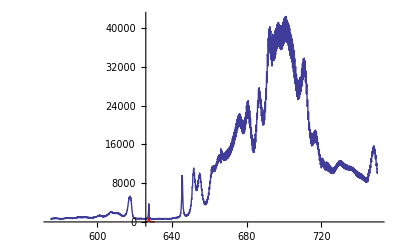
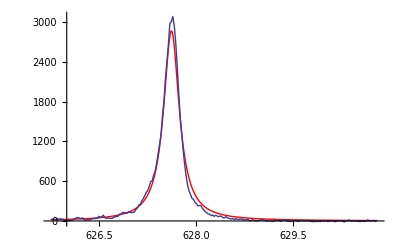
{10070_afterTE-1_0809a 18_03_24.csv, λ_center=627.618±0.00196648, γ_FWHM=-0.146408±0.00138827, Q=2142.39±20.5186,-Graphics-,-Graphics-}

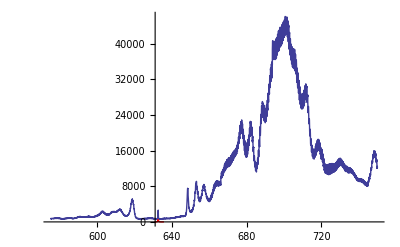
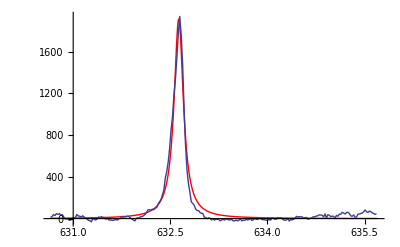
{10070_afterTE-1_0809b 18_05_21.csv, λ_center=632.63±0.00184208, γ_FWHM=0.0871808±0.00130688, Q=3629.26±53.586,-Graphics-,-Graphics-}

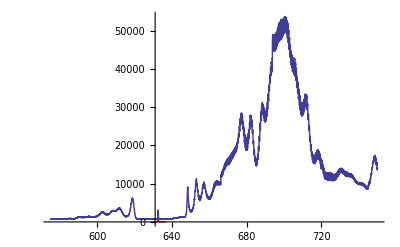
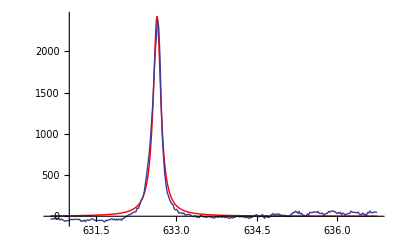
{10070_afterTE-1_0809b_reoptimized 18_08_05.csv, λ_center=632.637±0.00149848, γ_FWHM=0.0855884±0.00106342, Q=3696.81±45.3562,-Graphics-,-Graphics-}

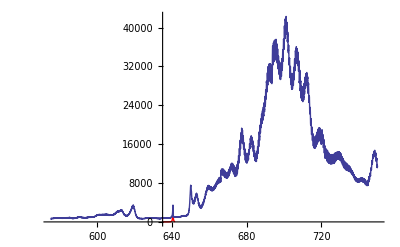
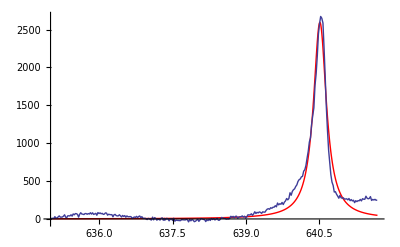
{10070_afterTE-1_0809d_reoptimized 18_12_20.csv, λ_center=640.52±0.00346933, γ_FWHM=0.161586±0.00245048, Q=1982.98±29.6079,-Graphics-,-Graphics-}

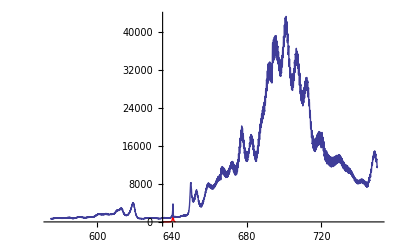
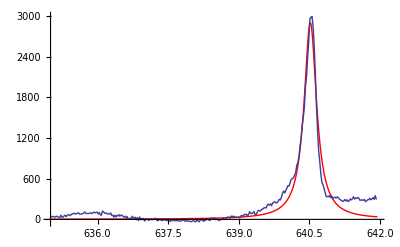
{10070_afterTE-1_0809d_reoptimized 18_15_45.csv, λ_center=640.523±0.00377944, γ_FWHM=-0.162052±0.00267178, Q=1975.28±33.1295,-Graphics-,-Graphics-}

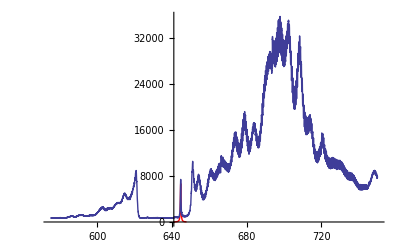
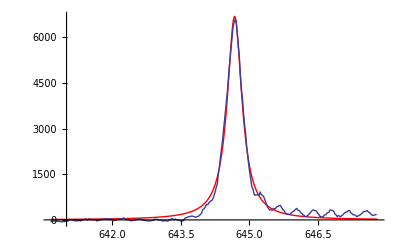
{10070_afterTE-1_0809e 18_20_00.csv, λ_center=644.676±0.00224669, γ_FWHM=-0.195608±0.00158708, Q=1646.88±13.4795,-Graphics-,-Graphics-}

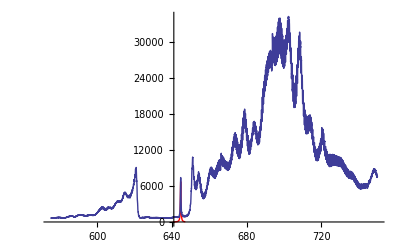
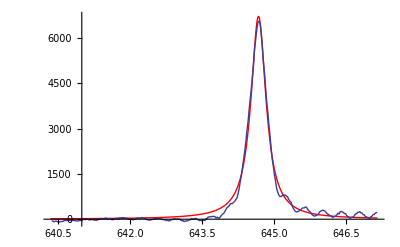
{10070_afterTE-1_0809e_BeforeComputerRestart 18_26_10.csv, λ_center=644.675±0.00202052, γ_FWHM=-0.189459±0.00142702, Q=1700.36±12.912,-Graphics-,-Graphics-}

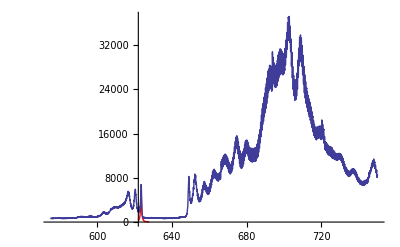
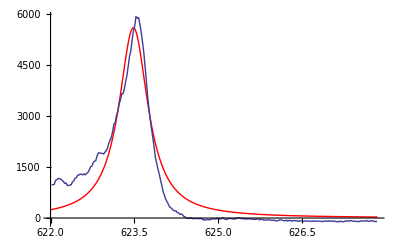
{10070_afterTE-1_0809f 18_23_42.csv, λ_center=623.483±0.0102599, γ_FWHM=0.316171±0.00719371, Q=986.99±21.9348,-Graphics-,-Graphics-}

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
ShowFits[Spectra,CoordList,fits,DataDir]
```